## Init

```mathematica
SetDirectory[NotebookDirectory[]];
(files=FileNames["data/*"])//TableForm
applyWithError[fct_,arg_]:=Module[{i,total,direction},
total=0;
(* calculate gauss error *)
direction=Table[0,{i,1,Length[arg]}];
For[i=1,i≤Length[arg],i++,
direction⟦i⟧=1;
total+=(((Derivative@@direction)[fct])@@arg⟦1;;,1⟧)^2*arg⟦i,2⟧^2;
direction⟦i⟧=0;
];
{fct@@arg⟦1;;,1⟧,Sqrt[total]}
]
weightedMean[vals_]:={Sum[vals⟦i,1⟧/vals⟦i,2⟧,{i,1,Length[vals]}]/Sum[1/vals⟦i,2⟧,{i,1,Length[vals]}],Sqrt[1/(Sum[1/vals⟦i,2⟧,{i,1,Length[vals]}])^2]}
toErrForm[{a_,b_}]:={(b+a)/2,Abs[b-a]/2};
<<"ErrorBarPlots`"
```

data\kalibrier.nb
data\M7_15C.TXT
data\M7_25C.TXT
data\M7_38C.TXT
data\M7ABS.TXT
data\M7_AN15.TX
data\M7_AN25.TX
data\M7_AN38.TX
data\M7EMSNON.TXT
data\M7EMSVES.TXT
data\M7_LT25.TX
data\M7_LT38.TX
data\mini.ods
data\placeholder.txt
data\temperatur2.ods
data\temperatur.ods

```mathematica
read[n_]:=Module[{dat},
str=OpenRead[files⟦n⟧];
dat={{},{}};
dat⟦1⟧=ReadList[str,Number,4];
ReadList[str,String,18];
dat⟦2⟧=ReadList[str,Number];
dat=Table[{dat⟦1⟧⟦3⟧+(i-1)*(dat⟦1⟧⟦4⟧-dat⟦1⟧⟦3⟧)/dat⟦1⟧⟦1⟧, dat⟦2⟧⟦i⟧},{i,1,Length@dat⟦2⟧}]
]
abs=read[5];
ves=read[10];
non={#⟦1⟧,#⟦2⟧/100}&/@read[9];
```

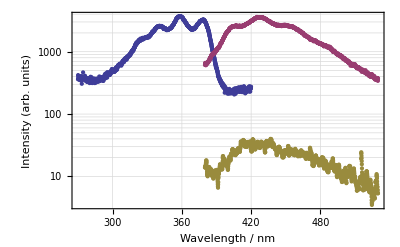

```mathematica
ListLogPlot[{abs,ves,non},Frame->True,Axes->None,FrameLabel->{"Wavelength / nm","Intensity (arb. units)"},GridLines->Automatic]
```

## fits, spectra

```mathematica
lg[x_,a_,s_,p_,x0_]:=a*E^(-s*p^2*Log[2]*(x-x0)^2)/(1+s*(1-p^2)(x-x0)^2);
fita=NonlinearModelFit[abs,
r1*x+r2+
lg[x,a1,s1,p,x01]+
lg[x,a2,s2,p,x02]+
lg[x,a3,s3,p,x03]+
lg[x,a4,s4,p,x04],
{{r1,0},{r2,0},{p,0},
{a1,2000},{s1,0.1},{x01,320},
{a2,2000},{s2,0.1},{x02,340},
{a3,2000},{s3,0.1},{x03,360},
{a4,2000},{s4,0.1},{x04,380}},
x
]
fita["ParameterConfidenceIntervalTable"]
```

FittedModel[814.283+(2763.03 2^(«1»))/(1+0.0307612 «1»)+(«1»)/(«1»)+«1»+(«1»)/(1+«1»)-2.08595 x]

| Estimate | Standard Error | Confidence Interval
r1 | -2.08595 | 0.0692114 | {-2.22171,-1.95018}
r2 | 814.283 | 25.0944 | {765.059,863.507}
p | 0. | 2.40748×10^-11 | {-4.72242×10^-11,4.72242×10^-11}
a1 | 941.415 | 22.5717 | {897.14,985.691}
s1 | 0.00801057 | 0.000543382 | {0.00694469,0.00907644}
x01 | 324.941 | 0.288115 | {324.376,325.506}
a2 | 1558.68 | 28.2504 | {1503.27,1614.1}
s2 | 0.0189599 | 0.00122527 | {0.0165565,0.0213633}
x02 | 340.142 | 0.0944714 | {339.957,340.328}
a3 | 3065.61 | 13.6542 | {3038.83,3092.4}
s3 | 0.0139892 | 0.000334089 | {0.0133339,0.0146445}
x03 | 358.648 | 0.0437669 | {358.562,358.734}
a4 | 2763.03 | 14.3409 | {2734.9,2791.16}
s4 | 0.0307612 | 0.00063463 | {0.0295164,0.0320061}
x04 | 377.959 | 0.0312853 | {377.898,378.02}

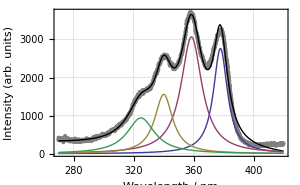

```mathematica
Show[
ListPlot[abs,PlotStyle->Gray],
Plot[Normal@fita,{x,270,420},PlotStyle->Black],
Plot[{lg[x,2763.0266615042096,0.030761222365159307,0,377.9588935473867],
lg[x,3065.613015244085,0.013989201795555023,0,358.6477290014585],lg[x,1558.683951031925,0.018959901290601953,0,340.1422222412903],lg[x,941.4154455439954,0.008010567341163807,0,324.94104403521084]
},{x,270,420},PlotRange->All],
Frame->True,Axes->None,FrameLabel->{"Wavelength / nm","Intensity (arb. units)"},GridLines->Automatic,
ImageSize->300
]
```

{{324.941,0.565155},{340.142,0.185312},{358.648,0.0858515},{377.959,0.061368}}

{{30774.8,53.5252},{29399.5,16.017},{27882.5,6.67439},{26457.9,4.29589}}

| Estimate | Standard Error | Confidence Interval
1 | 32216.4 | 37.2346 | {32056.2,32376.6}
x | -1433.18 | 21.2844 | {-1524.76,-1341.6}

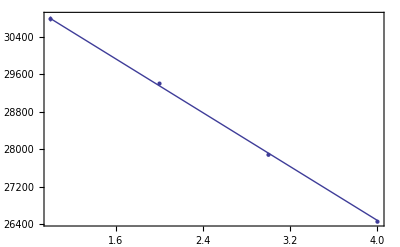

```mathematica
absPeaks=toErrForm/@{{324.3758889964019,325.5061990740198},{339.95691063599713,340.3275338465835},{358.56187751875063,358.7335804841664},{377.8975255113212,378.0202615834522}}
absPeaks=10^7/#&~applyWithError~{#}&/@absPeaks
(fitAbsP=LinearModelFit[Table[{i,absPeaks[[i,1]]},{i,1,4}],x,x,
Weights->absPeaks⟦1;;,2⟧])["ParameterConfidenceIntervalTable"]
Show[
ErrorListPlot[absPeaks,Frame->True,Axes->None],
Plot[Normal@fitAbsP,{x,1,4}]
]
```

```mathematica
fitv=NonlinearModelFit[ves,
r1*x+r2+
lg[x,a1,s1,p,x01]+
lg[x,a2,s2,p,x02]+
lg[x,a3,s3,p,x03]+
lg[x,a4,s4,p,x04],
{{r1,0},{r2,0},{p,0},
{a1,2000},{s1,0.1},{x01,400},
{a2,2000},{s2,0.1},{x02,425},
{a3,2000},{s3,0.1},{x03,450},
{a4,2000},{s4,0.1},{x04,490}},
x
]
fitv["ParameterConfidenceIntervalTable"]
```

FittedModel[-147.855+(584.217 2^(«1»))/(1+0.00189521 «1»)+«1»+«1»+(«1»)/(1+«1»)+0.508666 x]

| Estimate | Standard Error | Confidence Interval
r1 | 0.508666 | 0.0503835 | {0.409836,0.607497}
r2 | -147.855 | 23.2831 | {-193.526,-102.183}
p | 0. | 7.26341×10^-10 | {-1.42476×10^-9,1.42476×10^-9}
a1 | 1451.53 | 8.35706 | {1435.14,1467.92}
s1 | 0.0102415 | 0.000175013 | {0.00989822,0.0105848}
x01 | 403.744 | 0.0344498 | {403.676,403.811}
a2 | 2765.97 | 10.799 | {2744.79,2787.16}
s2 | 0.00449883 | 0.0000587975 | {0.00438349,0.00461416}
x02 | 426.858 | 0.0317485 | {426.795,426.92}
a3 | 1565.68 | 15.9509 | {1534.39,1596.97}
s3 | 0.00362688 | 0.0000944099 | {0.00344169,0.00381207}
x03 | 454.014 | 0.0675216 | {453.881,454.146}
a4 | 584.217 | 12.4687 | {559.759,608.675}
s4 | 0.00189521 | 0.000087202 | {0.00172416,0.00206626}
x04 | 482.985 | 0.313198 | {482.371,483.599}

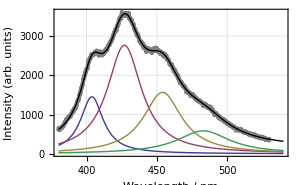

```mathematica
Show[
ListPlot[ves,PlotStyle->Gray],
Plot[Normal@fitv,{x,380,540},PlotStyle->Black],
Plot[{lg[x,1451.5,0.01024,0,403.744],
lg[x,2766,0.0044988,0,426.858],
lg[x,1566,0.00362688,0,454.014],
lg[x,584.2,0.00189521,0,482.985]},{x,380,540},PlotRange->All],
Frame->True,Axes->None,FrameLabel->{"Wavelength / nm","Intensity (arb. units)"},GridLines->Automatic,
ImageSize->300
]
```

{{403.744,0.0675755},{426.858,0.0622766},{454.014,0.132448},{482.985,0.614357}}

{{24768.2,4.14551},{23427.,3.4179},{22025.8,6.42551},{20704.6,26.3362}}

| Estimate | Standard Error | Confidence Interval
1 | 26117.3 | 32.5205 | {25977.4,26257.2}
x | -1354.16 | 9.26309 | {-1394.02,-1314.31}

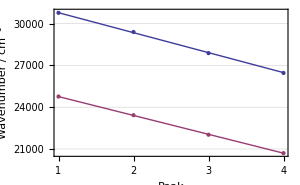

```mathematica
emsPeaks=toErrForm/@{{403.6761604273871,403.81131145289737},{426.79523820193987,426.9197914496539},{453.8810570280057,454.14595289798166},{482.3707436404949,483.5994572607357}}
emsPeaks=10^7/#&~applyWithError~{#}&/@emsPeaks
(fitEmsP=LinearModelFit[Table[{i,emsPeaks[[i,1]]},{i,1,4}],x,x,
Weights->emsPeaks⟦1;;,2⟧])["ParameterConfidenceIntervalTable"]
Show[
ErrorListPlot[{absPeaks,emsPeaks},Frame->True,Axes->None],
Plot[{Normal@fitAbsP,Normal@fitEmsP},{x,1,4}],FrameLabel->{"Peak","Wavenumber / cm^-1"},ImageSize->300,FrameTicks->{{Automatic,Automatic},{{1,2,3,4},None}},GridLines->{None,Automatic}
]
```

```mathematica
fitAbsP["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | 32216.4 | 37.2346 | {32056.2,32376.6}
x | -1433.18 | 21.2844 | {-1524.76,-1341.6}

```mathematica
omega=#*0.0299792&/@{{-1354.1624114301776,9.26308728810886},{-1433.1786939680214,21.284378744610304}}
```

{{-40.5967,0.2777},{-42.9656,0.638089}}

```mathematica
mc=1.99442*10^(-26);
hbar=1.054572*10^(-10);
(mc*(#*10^12)^2&~applyWithError~{#})&/@omega
(Sqrt[hbar/(mc*#*10^12)]&~applyWithError~{#})&/@Abs@omega
```

{{32.8699,0.44969},{36.8178,1.09357}}

{{11.4126,0.0390337},{11.0935,0.0823759}}

```mathematica
fitn=NonlinearModelFit[non,
r1*x+r2+
lg[x,a1,0.0102,0,403.7]+
lg[x,a2,0.00450,0,426.86]+
lg[x,a3,0.00363,0,454.0]+
lg[x,a4,0.00190,0,482.985],
{{r1,0},{r2,0},
{a1,20},
{a2,20},
{a3,20},
{a4,20}},
x
]
fitn["ParameterConfidenceIntervalTable"]
```

FittedModel[10.429+7.1912/(1+0.0019 («1»)^2)+(«18»)/(1+«1»)+«1»+(«18»)/(1+«7» «1»)-0.0112866 x]

| Estimate | Standard Error | Confidence Interval
r1 | -0.0112866 | 0.0033766 | {-0.01791,-0.00466325}
r2 | 10.429 | 1.64029 | {7.21151,13.6465}
a1 | 8.89744 | 0.516956 | {7.8834,9.91147}
a2 | 24.6736 | 0.375603 | {23.9368,25.4104}
a3 | 11.5179 | 0.345326 | {10.8405,12.1953}
a4 | 7.1912 | 0.397938 | {6.41063,7.97178}

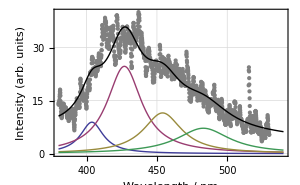

```mathematica
Show[
ListPlot[non,PlotStyle->Gray],
Plot[Normal@fitn,{x,380,540},PlotStyle->Black],
Plot[{lg[x,8.90,0.01024,0,403.744],
lg[x,24.7,0.0044988,0,426.858],
lg[x,11.52,0.00362688,0,454.014],
lg[x,7.19,0.00189521,0,482.985]},{x,380,540},PlotRange->All],
Frame->True,Axes->None,FrameLabel->{"Wavelength / nm","Intensity (arb. units)"},GridLines->Automatic,
ImageSize->300
]
```

```mathematica
n=(#1+#2+#3+#4)&~applyWithError~{{8.897,1.02},{24.674,0.8},{11.518,0.68},{7.191,0.78}}
v=(#1+#2+#3+#4)&~applyWithError~{{1451.53,14},{2766,27},{1566,26},{584,25}}//N
(#1/#2)&~applyWithError~{n,v}
(#2/#1)&~applyWithError~{n,v}
```

{52.28,1.65867}

{6367.53,47.1805}

{0.0082104,0.000267499}

{121.797,3.96819}

## init anisotropy

```mathematica
readA[n_]:=Module[{dat},
str=OpenRead[files⟦n⟧];
ReadList[str,String,3];
dat=ReadList[str,{Number,Number,Number,Number}]
]
readwtf[n_]:=Module[{dat},
str=OpenRead[files⟦n⟧];
ReadList[str,String,3];
dat= ReadList[str,{Number,Number,Number,Number,Number}]⟦1;;,2;;5⟧
]
a15=readA[2];
a25=readA[3];
a38=readwtf[4];
a15a=readA[6];
a25a=readA[7];
a38a=readA[8];
a25l=readA[11];
a38l=readA[12];
```

```mathematica
sum={a15⟦1,1⟧};
For[i=2,i<=Length@a15,++i,
AppendTo[sum,sum⟦i-1⟧+a15⟦i,1⟧];
]
```

```mathematica
stuff[dat_]:=Module[{fit1,fit2,w},
w=Table[Abs[(sum⟦i⟧^3)/(0.0000001+dat⟦i,3⟧*(dat⟦i,3⟧+sum⟦i⟧))],{i,40,Length@sum}];
fit1=NonlinearModelFit[(dat⟦1;;,3⟧/(sum+0.00000001))⟦40;;⟧,a E^(-b x)+r0,{{a,0.001},{b,0.001},{r0,0}},x,
Weights->w];
w=Table[Abs[(sum⟦i⟧^3)/(0.0000001+dat⟦i,4⟧*(dat⟦i,4⟧+sum⟦i⟧))],{i,40,Length@sum}];
fit2=NonlinearModelFit[(dat⟦1;;,4⟧/(sum+0.00000001))⟦40;;⟧,a E^(-b x)+r0,{{a,0.001},{b,0.001},{r0,0}},x,
Weights->w];
Print["b1= "<>ToString[({#⟦1⟧+#⟦2⟧,Abs[#⟦2⟧-#⟦1⟧]}/2)&@(fit1["ParameterConfidenceIntervals"]⟦2⟧)]];
Print["b2= "<>ToString[({#⟦1⟧+#⟦2⟧,Abs[#⟦2⟧-#⟦1⟧]}/2)&@fit2["ParameterConfidenceIntervals"]⟦2⟧]];
Print[fit1["RSquared"]];
Print@Show[
ListLogPlot[{(dat⟦1;;,3⟧/sum),(dat⟦1;;,4⟧/sum)},Joined->True,PlotRange->All,Frame->True,Axes->None,GridLines->Automatic,FrameLabel->{"Channel","Intensity (arb. units)"},ImageSize->350],
LogPlot[{Normal@fit1/.x->(y-50),Normal@fit2/.x->(y-50)},{y,0,255}]
];
{fit1,fit2}
]
```

b1= {0.00843907, 0.00253561}

b2= {0.0062813, 0.00303384}

0.961958

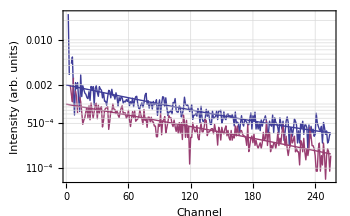

b1= {0.00650709, 0.00218178}

b2= {0.00874173, 0.00258256}

0.970146

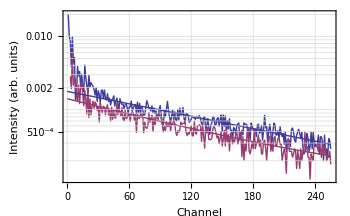

b1= {0.00874829, 0.00263535}

b2= {0.00996938, 0.00286615}

0.951823

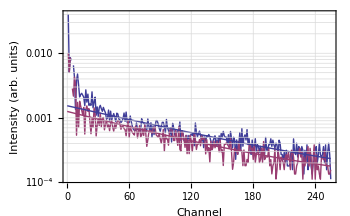

{{FittedModel[0.000139429+0.00121122 ⅇ^(-0.00843907 x)],FittedModel[-0.0000427113+0.000757807 ⅇ^(-0.0062813 x)]},{FittedModel[-2.386×10^-6+0.00128494 ⅇ^(-0.00650709 x)],FittedModel[0.0000915772+0.000852395 ⅇ^(-0.00874173 x)]},{FittedModel[0.0000768071+0.000943204 ⅇ^(-0.00874829 x)],FittedModel[0.000086781+0.000709833 ⅇ^(-0.00996938 x)]}}

```mathematica
fits=stuff/@{a15,a25,a38}
```

```mathematica
fits⟦1,1⟧["EstimatedVariance"]
```

1.17457

```mathematica
FullSimplify@(#1/#2&~applyWithError~{{m,Sqrt@m},{t,Sqrt[t]}})
```

{m/t,√((m (m+t))/t^3)}

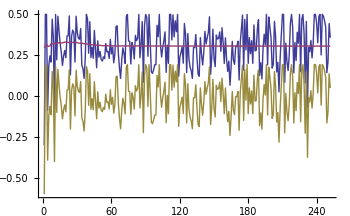
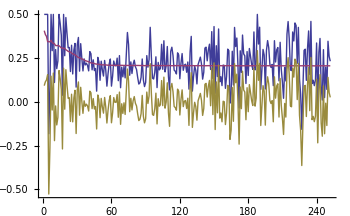
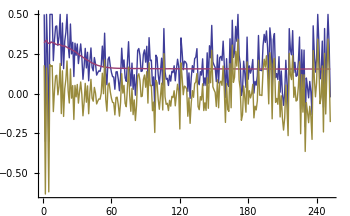

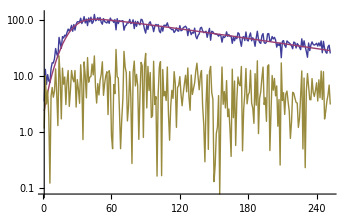
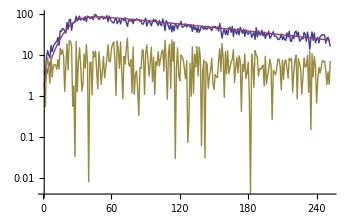

```mathematica
ListPlot[{#⟦1;;,2⟧,#⟦1;;,3⟧,#⟦1;;,4⟧},ImageSize->350,PlotRange->All,Joined->True]&/@{a15a,a25a,a38a}
ListLogPlot[Abs/@{#⟦1;;,2⟧,#⟦1;;,3⟧,#⟦1;;,4⟧},ImageSize->350,PlotRange->All,Joined->True]&/@{a25l,a38l}
```